```mathematica
(*modeling parameters*)
deltafreq=1;
maxfreq=400;
freqvec=Table[f,{f,1,maxfreq,deltafreq}];
fricker=30;

(*Add 0 frequency manually*)
freqs=Join[{0},freqvec];
```

```mathematica
(*source wavelet*)
rickerF[f_,fp_]:=Module[{ω=2Pi f,ωp=2Pi fp},(2 ω^2)/(√Pi ωp^3)Exp[-(ω/ωp)^2]//N]
srcF=rickerF[#,fricker]&/@freqs;
```

```mathematica
(*time vector*)
t=Range[Length[srcF]]/(deltafreq Length[srcF])//N;
```

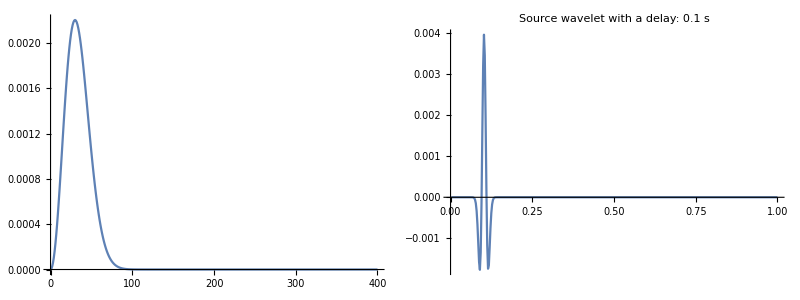

```mathematica
With[{delay=.1},
{{ListLinePlot[{freqs,srcF}ᵀ,PlotRange->Full,ImageSize->Medium],ListLinePlot[{t,Re@InverseFourier@(srcF (Exp[ⅈ 2Pi# delay]&/@freqs))}ᵀ,PlotRange->{Automatic,Full},PlotLabel->"Source wavelet with a delay: "<>ToString[delay]<>" s",ImageSize->Medium]}}//TableForm
]
```

```mathematica
(*import modeled data*)
gather=Uncompress@Import[NotebookDirectory[]<>"x0-5KM_dx25M.mc","String"];

(* pad with 0 *)
csgF=PadLeft[gather,Dimensions@gather+{1,0}];
```

```mathematica
xvec=Table[x0,{x0,0,5,.025}];

csg=InverseFourier[
csgF srcF
];
```

```mathematica
Manipulate[
ListPlot[{freqs,Abs@csgF[[;;,i]]}ᵀ,PlotRange->Full],{i,1,Length@xvec,1}]
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Transpose::nmtx: The first two levels of {freqs,Abs[Symbol[]]} cannot be transposed.

ListPlot::lpn: Transpose[{freqs,Abs[Symbol[]]}] is not a list of numbers or pairs of numbers.

```mathematica
Manipulate[
ListLinePlot[{t,Abs@csg[[;;,i]]}ᵀ,PlotRange->Full],{i,1,Length@xvec,1}]
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Transpose::nmtx: The first two levels of {t,Abs[Symbol[]]} cannot be transposed.

ListLinePlot::lpn: Transpose[{t,Abs[Symbol[]]}] is not a list of numbers or pairs of numbers.

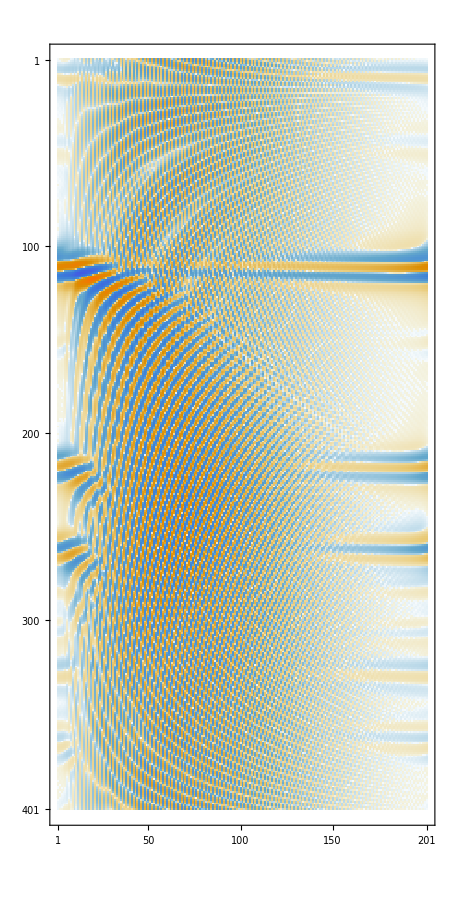

```mathematica
MatrixPlot[csg]
```